```mathematica
AugmentedFormula[form_,edge_,full_]:=ImpliedNodes[Map[SymbolReplace[#,edge]&,form],full]
```

```mathematica
DrawAugmented[form_]:=Block[{labels=Map[#[[1]]->Rotate[Labeled[SymbolToLabel[#[[1]]],Style[#[[2]],Red]],Pi/6]&,Tally[form]]},
Graph[FormulaGraphReverse2[form],VertexLabels->labels,ImageSize->650]
]
```

```mathematica
Sinks[g_]:=Select[VertexList[g],SymbolLevel[#]==4&]
```

```mathematica
AlmostSinks[g_]:=With[{s=Sinks[g]//First},Select[VertexList[VertexInComponent[g,s]],#=!=s&]]
```

```mathematica
AlmostSinks[g_]:=With[{s=Sinks[g]},DeleteDuplicates[Flatten[Table[Select[VertexInComponent[g,v,1],#=!=v&],{v,s}]]]]
```

```mathematica
With[{g=MinimalGraph[5]},
With[{full=FindFullFormula[g]},
{full,
Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]//Flatten//Tally
}
]
]
```

{{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46},{{v1x2x3x4x5x6,12},{v1x2x3x46x5,6},{v1x2x36x4x5,8},{v1x2x35x4x6,6},{v1x2x35x46,1}}}

```mathematica
AlmostSinks[FormulaGraphReverse2[FindFullFormula[MinimalGraph[6]]]]
```

{v1x2x357x46,v1x2x357x4x6,v1x2x35x46x7,v1x2x37x46x5,v1x2x3x46x57}

```mathematica
VertexInComponent[FormulaGraphReverse2[FindFullFormula[CycleGraph[6]]],v1x2x3x4x5x6,2]
```

{v1x2x3x4x5x6}

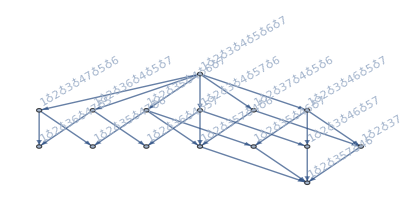
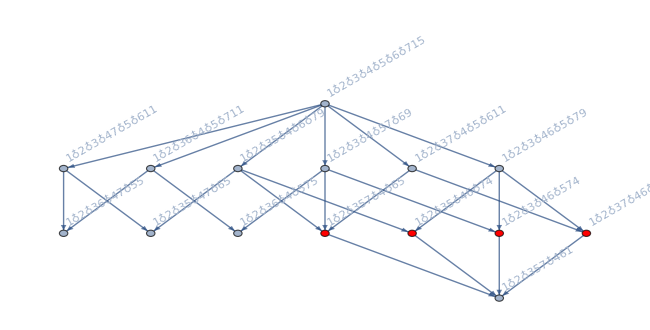
{-Graphics-,{v1x2x357x4x6,v1x2x35x46x7,v1x2x37x46x5,v1x2x3x46x57},{v1x2x357x46},-Graphics-}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
AlmostSinks[FormulaGraphReverse2[full]],
Sinks[FormulaGraphReverse[full]],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]
```

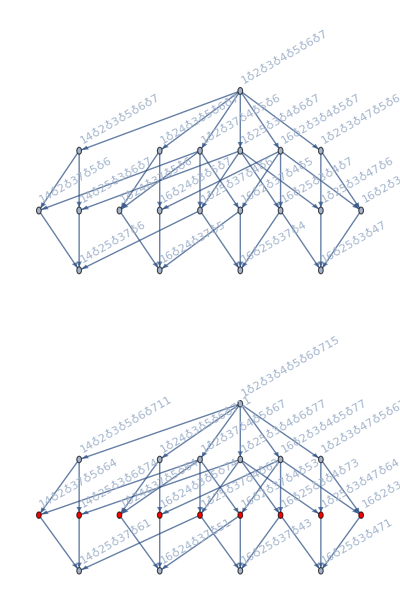

```mathematica
With[{g=ReadGrof[6]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

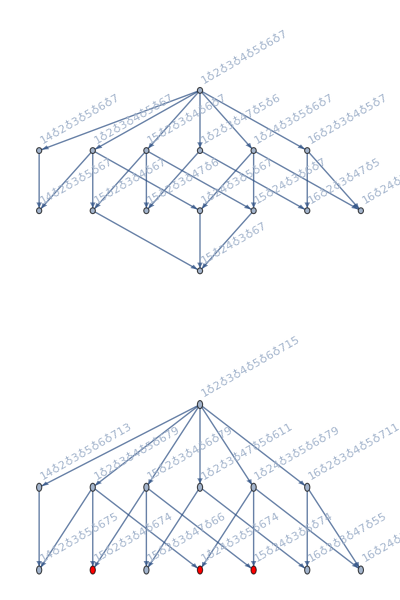

```mathematica
With[{g=ReadGrof[5]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

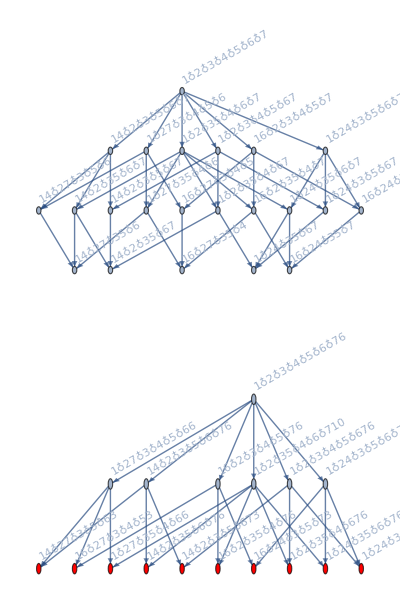

```mathematica
With[{g=ReadGrof[7]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[VertexContract[g,{e[[1]],e[[2]]}]],e,full],{e,EdgeList[GraphComplement[g]]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

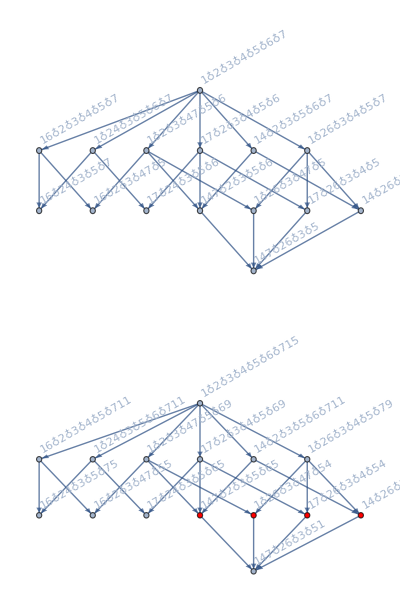

```mathematica
With[{g=ReadGrof[8]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

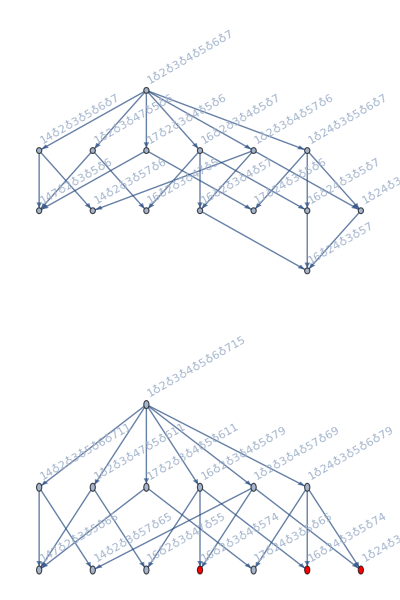

```mathematica
With[{g=ReadGrof[9]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```

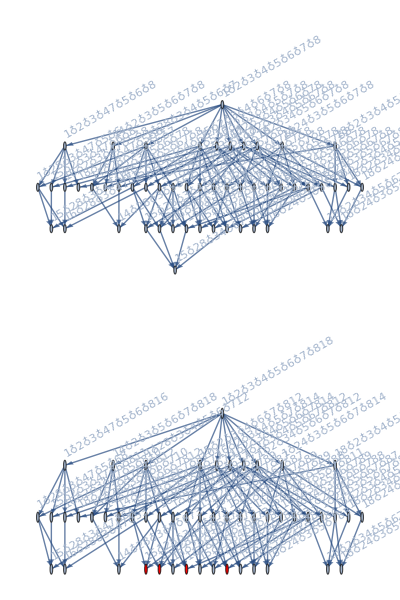

```mathematica
With[{g=ReadGrof[10]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],ImageSize->600],
Graph[DrawAugmented[Flatten[Table[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full],{e,EdgeList[g]}]]],VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]]
}
]
]//Column
```